```mathematica
data=Join[
Import["K:\\data\\2022\\11\\20221118\\fft\\box1_board1_step.csv","Table",HeaderLines->1],
Import["K:\\data\\2022\\11\\20221118\\fft\\box1_board2_step.csv","Table",HeaderLines->1],
Import["C:\\Users\\Ye Lab\\Desktop\\Cal\\current_fpga\\dac_lower_drive\\box1_board3_step_2.csv","Table",HeaderLines->1],Import["K:\\data\\2022\\11\\20221102\\fft\\board1_step.csv","Table",HeaderLines->1],
Import["K:\\data\\2022\\11\\20221102\\fft\\board2_step.csv","Table",HeaderLines->1],
Import["K:\\data\\2022\\11\\20221102\\fft\\board3_step.csv","Table",HeaderLines->1]];
startV=data[[All,1]];
maxV=data[[All,2]];
endV=data[[All,3]];
t10=data[[All,4]];
t50=data[[All,5]];
t90=data[[All,6]];
DACs=Table[i,{i,0,47}];
```

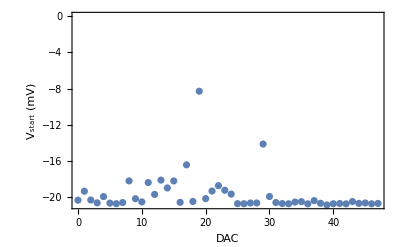

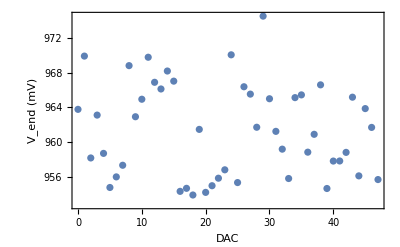

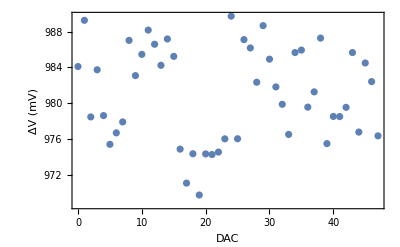

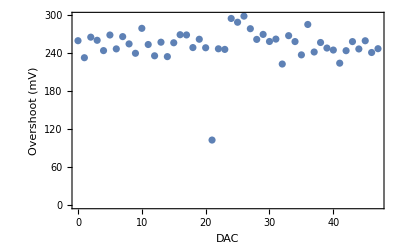

```mathematica
ListPlot[Transpose@{DACs,10^3 startV},Frame->True,FrameLabel->{"DAC","V_start (mV)"},PlotRange->All]
ListPlot[Transpose@{DACs,10^3 endV},Frame->True,FrameLabel->{"DAC","V_end (mV)"},PlotRange->All]
ListPlot[Transpose@{DACs,10^3(endV-startV)},Frame->True,FrameLabel->{"DAC","ΔV (mV)"},PlotRange->All]
ListPlot[Transpose@{DACs,10^3(maxV-endV)},Frame->True,FrameLabel->{"DAC","Overshoot (mV)"},PlotRange->All]
```

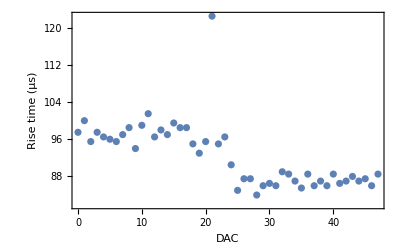

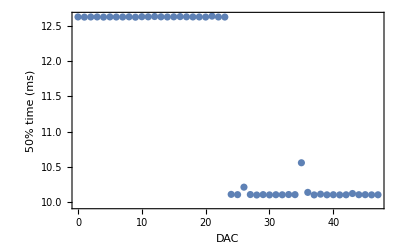

```mathematica
ListPlot[Transpose@{DACs,10^6(t90-t10)},Frame->True,FrameLabel->{"DAC","Rise time (μs)"},PlotRange->All]
ListPlot[Transpose@{DACs,10^3(t50)},Frame->True,FrameLabel->{"DAC","50% time (ms)"},PlotRange->All]
```